```mathematica
k = 3;
nwords = 12;
beta1=.5;
beta2 = .5;
choicesets = Subsets[Range[nwords],{k}];
(*s1=RandomSample[Range[nwords]];
s2=RandomSample[Range[nwords]];*)
s1={20,9,4,13,15,2,24,12,1,18,25,19};
s2={14,16,4,9,5,12,15,20,19,21,1,11};

innerSum[cs_,sub_,s1_,beta_]:=(-1)^Length[sub]*Total[Exp[beta*s1[[Complement[Range[nwords],cs]]]]]/(Total[Exp[beta*s1[[Complement[Range[nwords],cs]]]]]+Total[Exp[beta*s1[[sub]]]])

probOfCS [cs_,s1_,beta_]:=Sum[innerSum[cs,Subsets[cs][[i]],s1,beta],{i,Length[Subsets[cs]]}]

probSelection[q_,s2_,beta_]:=Exp[beta*s2[[q]]]/Total[Exp[beta*s2]]

f[q_,choicesets_,s1_,s2_,beta1_,beta2_]:=Sum[If [MemberQ[choicesets[[i]],q],probOfCS[choicesets[[i]],s1,beta1]*probSelection[FirstPosition[choicesets[[i]],q],Part[s2,choicesets[[i]]],beta2],0],{i,Length[choicesets]}]

(*DiscretePlot3D[f[1,choicesets,ReplacePart[s1,1->u],ReplacePart[s2,1->v],beta1, beta2],{u,1,14},{v,1,14}]*)

fmix[q_,s1_,s2_,beta1_,beta2_]:=Exp[beta1*s1[[q]]+beta2*s2[[q]]]/Total[Exp[beta1*s1+beta2*s2]]

fmixint[q_,s1_,s2_,coef1_,coef2_,coef3_]:=Exp[coef1*s1[[q]]+coef2*s2[[q]]+coef3*s1[[q]]*s2[[q]]]/Total[Exp[coef1*s1+coef2*s2+coef3*s1*s2]]

g[coef1_,coef2_,coef3_,beta1_,beta2_]:=Sum[Abs[f[i,choicesets,s1,s2,beta1,beta2]-fmixint[i,s1,s2,coef1,coef2,coef3]],{i,nwords}]

h[coef1_,coef2_,coef3_,beta1_,beta2_]:=Sum[Abs[fmix[i,s1,s2,beta1,beta2]-fmixint[i,s1,s2,coef1,coef2,coef3]],{i,nwords}]

NMinimize[g[coef1,coef2,coef3,beta1,beta2],{coef1,coef2,coef3}]

(*D[f[1,choicesets,s1,ReplacePart[s2,1->v],beta1,beta2],v]
DiscretePlot[Evaluate[D[f[1,choicesets,s1,ReplacePart[s2,1->v],beta1,beta2],{v,1}]],{v,1,14},PlotRange->Full]*)
```

{0.127424,{coef1→0.0499408,coef2→-0.209853,coef3→0.0195222}}

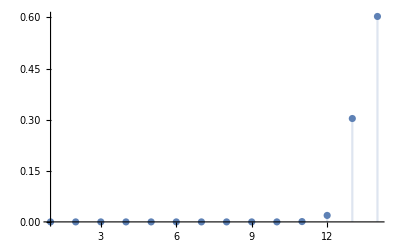

```mathematica
fmix[q_,s1_,s2_,beta1_,beta2_]:=Exp[beta1*s1[[q]]+beta2*s2[[q]]]/Total[Exp[beta1*s1+beta2*s2]]
DiscretePlot[Evaluate[D[fmix[1,s1,ReplacePart[s2,1->v],beta1,beta2],{v,1}]],{v,1,14},PlotRange->Full]
```